### The formulas, derivations and expressions, 1D

```mathematica
nEuler1D[ρm_,ξb_,dξ_]=-(2 dξ ⅇ^(-(2 (1+ρm))/ξb) (-2 ξb Hypergeometric0F1Regularized[1,(4 ρm)/ξb^2]+(ξb+4 ρm) Hypergeometric0F1Regularized[2,(4 ρm)/ξb^2]))/(√(2π) ξb^3 √(dξ ρm))
nEuler1DG[ρm_,ξb_,dξ_]=-Sqrt[dξ](ρm-1)Exp[-(ρm-1)^2/2/ξb]/(2 Pi ξb^(3/2))
```

-(dξ ⅇ^(-(2 (1+ρm))/ξb) √(2/π) (-2 ξb Hypergeometric0F1Regularized[1,(4 ρm)/ξb^2]+(ξb+4 ρm) Hypergeometric0F1Regularized[2,(4 ρm)/ξb^2]))/(ξb^3 √(dξ ρm))

-(√dξ ⅇ^(-(-1+ρm)^2/(2 ξb)) (-1+ρm))/(2 π ξb^(3/2))

```mathematica
(* construction of the function to be intergarted over λΔ for the computations of the extrema number densities *)
TL0[ρ_,φ0_,c0_,λc_]=c0 Exp[φ0-λc ρ] Hypergeometric0F1Regularized[2,c0 ρ];
TL1[ρ_,φ0_,c0_,λc_]=φ0 TL0[ρ,φ0,c0,λc]+c0 D[TL0[ρ,φ0,c0,λc],c0]//FullSimplify;
fc[λΔ_,dξ_]=(1+dξ λΔ/2)^2;
ϕextrem[ρ_,λΔ_,ξb_,dξ_,vξ_]=(√(1-dξ λΔ))/(√(2  π dξ ρ))TL0[ρ,-2/ξb,(2/ξb)^2 fc[λΔ,dξ],2/ξb fc[λΔ,dξ]-vξ λΔ^2/2]//FullSimplify
bϕextrem[ρ_,λΔ_,ξb_,dξ_,vξ_]=(√(1-dξ λΔ))/(√(2 π dξ ρ))TL1[ρ,-2/ξb,(2/ξb)^2 fc[λΔ,dξ],2/ξb fc[λΔ,dξ]-vξ λΔ^2/2]//FullSimplify
```

(ⅇ^(-(4+((2+dξ λΔ)^2-vξ λΔ^2 ξb) ρ)/(2 ξb)) √(1-dξ λΔ) (2+dξ λΔ)^2 Hypergeometric0F1Regularized[2,((2+dξ λΔ)^2 ρ)/ξb^2])/(√(2 π) ξb^2 √(dξ ρ))

1/(√(2 π) ξb^3 √(dξ ρ))ⅇ^(-(4+((2+dξ λΔ)^2-vξ λΔ^2 ξb) ρ)/(2 ξb)) √(1-dξ λΔ) (2+dξ λΔ)^2 (ξb Hypergeometric0F1Regularized[1,((2+dξ λΔ)^2 ρ)/ξb^2]-2 Hypergeometric0F1Regularized[2,((2+dξ λΔ)^2 ρ)/ξb^2])

```mathematica
nϕEuler1D[ρ_,ξb_,dξ_]=((D[ϕextrem[ρ,λΔ,ξb,dξ,vξ],λΔ])/.λΔ->0)//FullSimplify;
nϕEuler1D[ρ,ξb,dξ]-nEuler1D[ρ,ξb,dξ]//FullSimplify
```

0

```mathematica
bnEuler1D[ρ_,ξb_,dξ_]=((D[bϕextrem[ρ,λΔ,ξb,dξ,vξ],λΔ])/.λΔ->0)//FullSimplify
```

(dξ ⅇ^(-(2 (1+ρ))/ξb) √(2/π) (ξb (ξb-4 (1+ρ)) Hypergeometric0F1[1,(4 ρ)/ξb^2]+2 (ξb+8 ρ) Hypergeometric0F1[2,(4 ρ)/ξb^2]))/(ξb^4 √(dξ ρ))

```mathematica
nEuler1DG[1.04,.02,dξ]
nEuler1D[1.04,.02,dξ]
```

-2.16254 √dξ

-2.33321 √dξ

```mathematica
Clear[nmin1D,bnmin1D]
nmin1D[ρ_,ξb_,dξ_,vξ_]:=nmin1D[ρ,ξb,dξ,vξ]=NIntegrate[ϕextrem[ρ,I λΔ+1,ξb,dξ,vξ]/((I λΔ+1)^2)/(2 Pi),{λΔ,-Infinity,Infinity}]
bnmin1D[ρ_,ξb_,dξ_,vξ_]:=bnmin1D[ρ,ξb,dξ,vξ]:=NIntegrate[bϕextrem[ρ,I λΔ+1,ξb,dξ,vξ]/((I λΔ+1)^2)/(2 Pi),{λΔ,-Infinity,Infinity}]
```

```mathematica
Clear[nmax1D,bnmax1D]
nmax1D[ρ_,ξb_,dξ_,vξ_]:=nmax1D[ρ,ξb,dξ,vξ]=NIntegrate[ϕextrem[ρ,I λΔ-1,ξb,dξ,vξ]/((I λΔ-1)^2)/(2 Pi),{λΔ,-Infinity,Infinity}]
bnmax1D[ρ_,ξb_,dξ_,vξ_]:=bnmax1D[ρ,ξb,dξ,vξ]=NIntegrate[bϕextrem[ρ,I λΔ-1,ξb,dξ,vξ]/((I λΔ-1)^2)/(2 Pi),{λΔ,-Infinity,Infinity}]
```

```mathematica
listρ=Table[10^li,{li,-.8,.8,.05}];
```

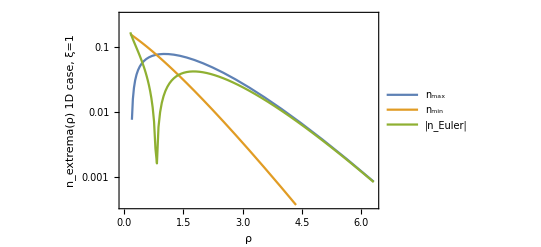

```mathematica
{Table[{ρ,nmax1D[ρ,1,.45,1.]//Re},{ρ,listρ}],Table[{ρ, nmin1D[ρ,1,.45,1.]//Re},{ρ,listρ}],Table[{ρ,nEuler1D[ρ,1,.45]//Re//Abs},{ρ,Table[10^li,{li,-0.8,.8,.02}]}]}//ListLogPlot[#,InterpolationOrder->1,Frame->True,Joined->True,
FrameLabel->{"ρ","n_extrema(ρ) 1D case, ξ̄=1"},PlotLegends->{"n_max","n_min","|n_Euler|"},PlotRange->{-.007,.3}]&
```

```mathematica
listρa=Table[10^li,{li,-.2,.8,.05}];
listρi=Table[10^li,{li,-.2,.8,.05}];
listρe=Table[10^li,{li,.1,.8,.05}];
```

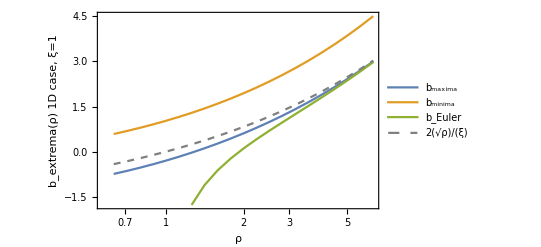

```mathematica
{Table[{ρ,bnmax1D[ρ,1,.45,1.]/nmax1D[ρ,1,.45,1.]//Re},{ρ,listρa}],Table[{ρ,( bnmin1D[ρ,1,.45,1.]/nmin1D[ρ,1,.45,1.])//Re},{ρ,listρi}],Table[{ρ,bnEuler1D[ρ,1,.45]/nEuler1D[ρ,1,.45]//Re},{ρ,listρe}],Table[{ρ,2 (Sqrt[ρ]-1)},{ρ,listρa}]}//ListLogLinearPlot[#,InterpolationOrder->1,Frame->True,Joined->True,PlotStyle->{Medium,Medium,Medium,{Dashed,Gray}},
FrameLabel->{"ρ","b_extrema(ρ) 1D case, ξ̄=1"},PlotLegends->{"b_maxima","b_minima","b_Euler","2(√ρ)/(ξ̄)"}]&
(*Export[NotebookDirectory[]<>"Bias_Extrema_2D_xb1.pdf",%]*)
```

### The formulas, 2D

```mathematica
(* Assumptions->{dξ>0,ξb>0, 8 vξ>dξ^2/ξb} *)
ac[λΔ_,λγ_,ξb_,dξ_,vξ_]=(2/ξb)^2((1+dξ λΔ/2)^2 );
λc[λΔ_,λγ_,ξb_,dξ_,vξ_]=2/ξb((1+dξ λΔ/2)^2-(1/12)vξ ξb(λγ^2+2λΔ^2));
ϕextrem2D[ρ_,λΔ_,λγ_,ξb_,dξ_,vξ_]=TL0[ρ,-2/ξb,ac[λΔ,λγ,ξb,dξ,vξ],λc[λΔ,λγ,ξb,dξ,vξ]](Pi √(4-4 dξ λΔ+dξ^2 (-λγ^2+λΔ^2)))/(dξ ρ (2 Pi)^2)
bϕextrem2D[ρ_,λΔ_,λγ_,ξb_,dξ_,vξ_]=TL1[ρ,-2/ξb,ac[λΔ,λγ,ξb,dξ,vξ],λc[λΔ,λγ,ξb,dξ,vξ]](Pi √(4-4 dξ λΔ+dξ^2 (-λγ^2+λΔ^2)))/(dξ ρ (2 Pi)^2)//FullSimplify
```

(ⅇ^(-2/ξb-(2 ((1+(dξ λΔ)/2)^2-1/12 vξ (λγ^2+2 λΔ^2) ξb) ρ)/ξb) (1+(dξ λΔ)/2)^2 √(4-4 dξ λΔ+dξ^2 (-λγ^2+λΔ^2)) Hypergeometric0F1Regularized[2,(4 (1+(dξ λΔ)/2)^2 ρ)/ξb^2])/(dξ π ξb^2 ρ)

1/(4 dξ π ξb^3 ρ)ⅇ^((-12-3 (2+dξ λΔ)^2 ρ+vξ (λγ^2+2 λΔ^2) ξb ρ)/(6 ξb)) (2+dξ λΔ)^2 √(-((2+dξ (λγ-λΔ)) (-2+dξ (λγ+λΔ)))) (ξb Hypergeometric0F1Regularized[1,((2+dξ λΔ)^2 ρ)/ξb^2]-2 Hypergeometric0F1Regularized[2,((2+dξ λΔ)^2 ρ)/ξb^2])

```mathematica
nEuler2D[ρ_,ξb_,dξ_]=((D[ϕextrem2D[ρ,λΔ,λγ,ξb,dξ,vξ],{λΔ,2}]-1/λγ D[ϕextrem2D[ρ,λΔ,λγ,ξb,dξ,vξ],{λγ,1}]-D[ϕextrem2D[ρ,λΔ,λγ,ξb,dξ,vξ],{λγ,2}]//Simplify)/.{λΔ->0,λγ->0})//FullSimplify
```

1/(π ξb^5)2 dξ ⅇ^(-(2 (1+ρ))/ξb) (ξb (4-3 ξb+4 ρ) Hypergeometric0F1Regularized[2,(4 ρ)/ξb^2]-2 (ξb+8 ρ) Hypergeometric0F1Regularized[3,(4 ρ)/ξb^2])

```mathematica
nEuler2DG[ρm_,ξb_,dξ_]=-(dξ ⅇ^(-(-1+ρm)^2/(2 ξb)) (ξb-(-1+ρm)^2))/(2 √2 π^(3/2) ξb^(5/2));
```

```mathematica
bnEuler2D[ρ_,ξb_,dξ_]=((D[bϕextrem2D[ρ,λΔ,λγ,ξb,dξ,vξ],{λΔ,2}]-1/λγ D[bϕextrem2D[ρ,λΔ,λγ,ξb,dξ,vξ],{λγ,1}]-D[bϕextrem2D[ρ,λΔ,λγ,ξb,dξ,vξ],{λγ,2}]//Simplify)/.{λΔ->0,λγ->0})//FullSimplify
```

1/(π ξb^5 ρ)2 dξ ⅇ^(-(2 (1+ρ))/ξb) (ξb (ξb-3 ξb ρ+4 ρ (3+ρ)) Hypergeometric0F1Regularized[1,(4 ρ)/ξb^2]-(ξb^2+8 ρ (1+3 ρ)) Hypergeometric0F1Regularized[2,(4 ρ)/ξb^2])

```mathematica
Clear[nmax2D,nmin2D]
nmax2D[ρ_,ξb_,dξ_,vξ_]:=nmax2D[ρ,ξb,dξ,vξ]=NIntegrate[ϕextrem2D[ρ,I λκ-1,I λγ,ξb,dξ,vξ](12 π λγ)/((λγ^2+(I λκ-1)^2)^(5/2))/(2 Pi)^2,{λκ,-∞,∞},{λγ,0,∞}]
nmin2D[ρ_,ξb_,dξ_,vξ_]:=nmin2D[ρ,ξb,dξ,vξ]=NIntegrate[ϕextrem2D[ρ,I λκ+1,I λγ,ξb,dξ,vξ](12 π λγ)/((λγ^2+(I λκ+1)^2)^(5/2))/(2 Pi)^2,{λκ,-∞,∞},{λγ,0,∞}]
```

```mathematica
nsaddle[ρ_,ξb_,dξ_,vξ_]:=nmax2D[ρ,ξb,dξ,vξ]+nmin2D[ρ,ξb,dξ,vξ]-nEuler2D[ρ,ξb,dξ]
```

```mathematica
Clear[bnmax2D,bnmin2D]
bnmax2D[ρ_,ξb_,dξ_,vξ_]:=bnmax2D[ρ,ξb,dξ,vξ]=NIntegrate[bϕextrem2D[ρ,I λκ-1,I λγ,ξb,dξ,vξ](12 π λγ)/((λγ^2+(I λκ-1)^2)^(5/2))/(2 Pi)^2,{λκ,-∞,∞},{λγ,0,∞}]
bnmin2D[ρ_,ξb_,dξ_,vξ_]:=bnmin2D[ρ,ξb,dξ,vξ]=NIntegrate[bϕextrem2D[ρ,I λκ+1,I λγ,ξb,dξ,vξ](12 π λγ)/((λγ^2+(I λκ+1)^2)^(5/2))/(2 Pi)^2,{λκ,-∞,∞},{λγ,0,∞}]
```

```mathematica
bnsaddle[ρ_,ξb_,dξ_,vξ_]:=bnmax2D[ρ,ξb,dξ,vξ]+bnmin2D[ρ,ξb,dξ,vξ]-bnEuler2D[ρ,ξb,dξ]
```

```mathematica
listρ=Table[10^li,{li,-.8,.8,.05}];
```

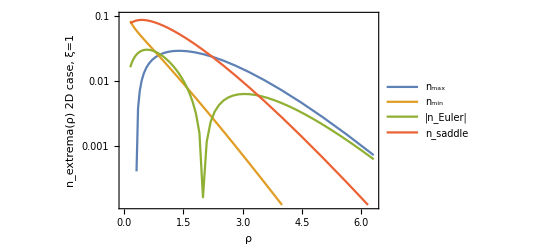

```mathematica
{Table[{ρ,nmax2D[ρ,1,.45,1.5]//Re},{ρ,listρ}],Table[{ρ, nmin2D[ρ,1,.45,1.5]//Re},{ρ,listρ}],Table[{ρ,nEuler2D[ρ,1,.45]//Re//Abs},{ρ,Table[10^li,{li,-0.8,.8,.02}]}],Table[{ρ,nsaddle[ρ,1,.45,1.5]//Re},{ρ,listρ}]}//ListLogPlot[#,InterpolationOrder->1,Frame->True,Joined->True,
FrameLabel->{"ρ","n_extrema(ρ) 2D case, ξ̄=1"},PlotLegends->{"n_max","n_min","|n_Euler|","n_saddle"},PlotRange->{-.005,.1}]&
```

```mathematica
listρa=Table[10^li,{li,.2,1.2,.05}];
listρi=Table[10^li,{li,-.4,1.2,.05}];
listρe=Table[10^li,{li,.45,1.2,.05}];
listρs=Table[10^li,{li,-.1,1.2,.05}];
```

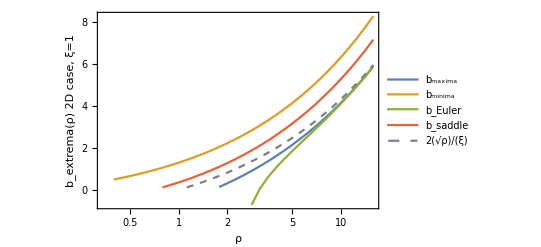

```mathematica
{Select[Table[{ρ,bnmax2D[ρ,1,.45,1.5]/nmax2D[ρ,1,.45,1.5]//Re},{ρ,listρa}],#[[2]]>0&],Table[{ρ, bnmin2D[ρ,1,.45,1.5]/nmin2D[ρ,1,.45,1.5]//Re},{ρ,listρi}],Table[{ρ,bnEuler2D[ρ,1,.45]/nEuler2D[ρ,1,.45]//Re},{ρ,listρe}],Table[{ρ,bnsaddle[ρ,1,.45,1.5]/nsaddle[ρ,1,.45,1.5]//Re},{ρ,listρs}]//Select[#,#[[2]]>0&]&,Table[{ρ,2 (Sqrt[ρ]-1)},{ρ,listρs}]//Select[#,#[[2]]>0&]&}//ListLogLinearPlot[#,InterpolationOrder->1,Frame->True,Joined->True,PlotStyle->{Medium,Medium,Medium,Medium,{Dashed,Gray},{Dotted,Gray}},
FrameLabel->{"ρ","b_extrema(ρ) 2D case, ξ̄=1"},PlotLegends->{"b_maxima","b_minima","b_Euler","b_saddle","2(√ρ)/(ξ̄)"}]&
```

### The formulas, 3D

```mathematica
nEuler3D[ρm_,ξb_,dξ_]=-1/(2 Sqrt[2] π^(3/2) ξb^5 ρm^3)ⅇ^(-(2 (1+ρm))/ξb) (dξ ρm)^(3/2) (-ξb (3 ξb^2+16 ρm (1+3 ρm)) Hypergeometric0F1Regularized[1,(4 ρm)/ξb^2]+(3 ξb^3+16 ξb ρm+6 ξb^2 ρm+32 ρm^2 (3+ρm)) Hypergeometric0F1Regularized[2,(4 ρm)/ξb^2])
nEuler3DG[ρm_,ξb_,dξ_]=-(dξ^(3/2) ⅇ^(-(-1+ρm)^2/(2 ξb)) (-3 ξb+(-1+ρm)^2) (-1+ρm))/(4 π^2 ξb^(7/2))
```

-1/(2 √2 π^(3/2) ξb^5 ρm^3)ⅇ^(-(2 (1+ρm))/ξb) (dξ ρm)^(3/2) (-ξb (3 ξb^2+16 ρm (1+3 ρm)) Hypergeometric0F1Regularized[1,(4 ρm)/ξb^2]+(3 ξb^3+16 ξb ρm+6 ξb^2 ρm+32 ρm^2 (3+ρm)) Hypergeometric0F1Regularized[2,(4 ρm)/ξb^2])

-(dξ^(3/2) ⅇ^(-(-1+ρm)^2/(2 ξb)) (-3 ξb+(-1+ρm)^2) (-1+ρm))/(4 π^2 ξb^(7/2))

### Plots of Euler number densities as a function of cumulative probs.

```mathematica
PDFG[ρ_,ξb_]=Exp[-(ρ-1)^2/2/ξb]/Sqrt[2 Pi ξb];
PDFNL[ρ_, ξb_] = (4*Hypergeometric0F1Regularized[2, (4*ρ)/ξb^2])/
     (E^((2*(1 + ρ))/ξb)*ξb^2);
```

```mathematica
Clear[cnEuler1DG,cnEuler2DG,cnEuler3DG]
cPDFG[ρ_,ξb_]=Integrate[PDFG[ρm,ξb],{ρm,-Infinity,ρ},Assumptions->{ξb>0}];
cnEuler1DG[ρ_,ξb_,dξ_]=Integrate[nEuler1DG[ρm,ξb,dξ],{ρm,-Infinity,ρ},Assumptions->{ξb>0}]
cnEuler2DG[ρ_,ξb_,dξ_]=Integrate[nEuler2DG[ρm,ξb,dξ],{ρm,-Infinity,ρ},Assumptions->{ξb>0}]
cnEuler3DG[ρ_,ξb_,dξ_]=Integrate[nEuler3DG[ρm,ξb,dξ],{ρm,-Infinity,ρ},Assumptions->{ξb>0}]
```

(ⅇ^(-(-1+ρ)^2/(2 ξb)) √(dξ/ξb))/(2 π)

-(dξ ⅇ^(-(-1+ρ)^2/(2 ξb)) (-1+ρ))/(2 √2 π^(3/2) ξb^(3/2))

(dξ^(3/2) ⅇ^(-(-1+ρ)^2/(2 ξb)) (-ξb+(-1+ρ)^2))/(4 π^2 ξb^(5/2))

```mathematica
Clear[cPDFNL,cnEuler1D,cnEuler2D,cnEuler3D]
cPDFNL[ρ_,ξb_]:=cPDFNL[ρ,ξb]=NIntegrate[PDFNL[ρm, ξb],{ρm,0.,ρ}]+Exp[-2/ξb]
cnEuler1D[ρ_,ξb_,dξ_]:=cnEuler1D[ρ,ξb,dξ]=NIntegrate[nEuler1D[ρm,ξb,dξ],{ρm,0.,ρ}];
cnEuler2D[ρ_,ξb_,dξ_]:=cnEuler2D[ρ,ξb,dξ]=dξ Exp[-2/ξb]/ξb^2/( Pi)+NIntegrate[nEuler2D[ρm,ξb,dξ],{ρm,0.,ρ}];cnEuler3D[ρ_,ξb_,dξ_]:=cnEuler3D[ρ,ξb,dξ]=NIntegrate[nEuler3D[ρm,ξb,dξ],{ρm,0.,ρ}];
```

```mathematica
Color1=RGBColor[94./255,129./255,182./255];
Color2=RGBColor[225./255,156./255,36./255];
Color3=RGBColor[143./255,176./255,50./255];
Color4=RGBColor[235./255,98./255,53./255];
Color5=RGBColor[135./255,120./255,179./255];

LColor1=Color1//Lighter//Lighter//Lighter;
LColor2=Color2//Lighter//Lighter//Lighter;
LColor3=Color3//Lighter//Lighter//Lighter;
LColor4=Color4//Lighter//Lighter//Lighter;
```

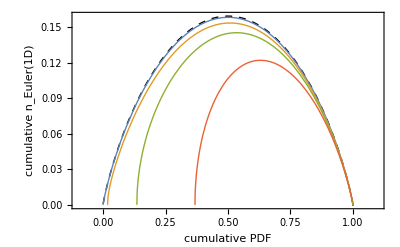

```mathematica
ParametricPlot[{{cPDFG[ρm+4,.1],cnEuler1DG[ρm+4,.1,.1]},{cPDFNL[ρm+4,.1], cnEuler1D[ρm+4,.1,.1]},{cPDFNL[ρm+4,.5],cnEuler1D[ρm+4,.5,.5]},{cPDFNL[ρm+4,1.],cnEuler1D[ρm+4,1.,1.]},{cPDFNL[ρm+4,2.],cnEuler1D[ρm+4,2.,2.]}},{ρm,-4,4},Frame->True,AspectRatio->1/GoldenRatio,PlotStyle->{{Thick,Dashed,Black},{Thick,Color1},{Thick,Color2},{Thick,Color3},{Thick,Color4},{Dashed,Color4}},LabelStyle->{Bold,Medium},FrameLabel->{"cumulative PDF","cumulative n_Euler(1D)"},PlotRange->{{-.1,1.1},Automatic}]
```

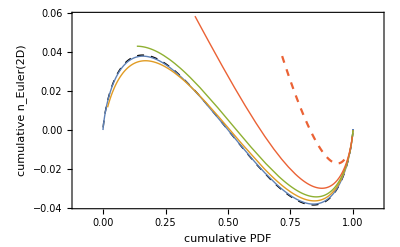

```mathematica
ParametricPlot[{{cPDFG[ρm+4,.1],cnEuler2DG[ρm+4,.1,.1]},{cPDFNL[ρm+4,.1],cnEuler2D[ρm+4,.1,.1]},{cPDFNL[ρm+4,.5],cnEuler2D[ρm+4,.5,.5]},{cPDFNL[ρm+4,1.],cnEuler2D[ρm+4,1.,1.]},{cPDFNL[ρm+4,2.],cnEuler2D[ρm+4,2.,2.]},{cPDFNL[ρm+4,6.],cnEuler2D[ρm+4,6.,6.]}},{ρm,-4,4},Frame->True,AspectRatio->1/GoldenRatio,PlotStyle->{{Thick,Dashed,Black},{Thick,Color1},{Thick,Color2},{Thick,Color3},{Thick,Color4},{Dashed,Color4}},LabelStyle->{Bold,Medium},FrameLabel->{"cumulative PDF","cumulative n_Euler(2D)"},PlotRange->{{-.1,1.1},All}]
```

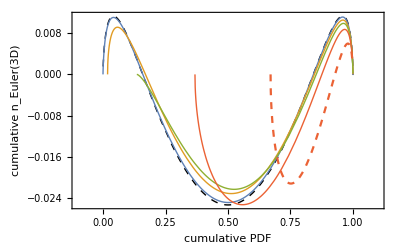

```mathematica
ParametricPlot[{{cPDFG[ρm+4,.1], cnEuler3DG[ρm+4,.1,.1]},{cPDFNL[ρm+4,.1],cnEuler3D[ρm+4,.1,.1]},{cPDFNL[ρm+4,.5],cnEuler3D[ρm+4,.5,.5]},{cPDFNL[ρm+4,1.],cnEuler3D[ρm+4,1.,1.]},{cPDFNL[ρm+4,2.],cnEuler3D[ρm+4,2.,2.]},{cPDFNL[2 ρm+8,5.],cnEuler3D[2 ρm+8,5.,5.]}},{ρm,-4,4},Frame->True,AspectRatio->1/GoldenRatio,PlotStyle->{{Thick,Dashed,Black},{Thick,Color1},{Thick,Color2},{Thick,Color3},{Thick,Color4},{Dashed,Color4}},LabelStyle->{Bold,Medium},FrameLabel->{"cumulative PDF","cumulative n_Euler(3D)"},PlotRange->{{-.1,1.1},All}]
```